```mathematica
SetDirectory["L:/moose/project2/trunk/elk"]
```

L:\moose\project2\trunk\elk

```mathematica
pWaterInit=0;
pOilInit=15;
viscOil=2/1000;
viscWater=viscOil/2;
densWater=10;
densOil=20;
qq=1/densWater;
porosity=1/4;
permeability=1/100000;

scaleRatio=2*1000;
beta=-Sqrt[porosity/permeability/scaleRatio];
delta=qq*viscOil/porosity/(viscOil-viscWater);
alpha=-beta^2*qq*viscOil*viscWater/porosity/(viscOil-viscWater)^2;
gamma=-beta*viscOil/(viscOil-viscWater);

gravity=0;
epsilon=permeability*(densOil-densWater)*gravity/qq/viscOil;
alphaPrime=alpha*(1-epsilon*gamma/beta);

deltaStar=beta/porosity/(viscOil-viscWater)*(permeability*(densWater-densOil)*gravity*(viscOil+viscWater)/(viscOil-viscWater)-qq*viscWater);

ClearAll[seff];
seff[pc_,shift_,scale_]:=1/Sqrt[1+Exp[(pc-shift)/scale]];
sWaterInit=seff[pOilInit-pWaterInit,10,(1/4)*scaleRatio*viscOil];
sOilInit=1-sWaterInit;

epsilonStar=alphaPrime*permeability*(densWater-densOil)*gravity/porosity/(viscOil-viscWater);
betaStar=-alphaPrime/beta/(sOilInit+gamma/beta);

short=Sqrt[deltaStar^2/4-epsilonStar];
short2=deltaStar/2-betaStar;

ClearAll[sStar,sStarPrime,sOil,z];
sStar[z_,t_]:=(1/2)Exp[-(deltaStar*z/2)-epsilonStar*t]*(Exp[z*short]*Erfc[z/2/Sqrt[t]+Sqrt[t]*short]+Exp[-z*short]*Erfc[z/2/Sqrt[t]-Sqrt[t]*short])-(1/2)Exp[(betaStar^2-betaStar*deltaStar)*t]*(Exp[-betaStar*z]*Erfc[z/2/Sqrt[t]+short2*Sqrt[t]]+Exp[(betaStar-deltaStar)z]*Erfc[z/2/Sqrt[t]-short2*Sqrt[t]])+Exp[-betaStar*z+(betaStar^2-betaStar*deltaStar)*t];
sStarPrime[z_,t_]:=Evaluate[D[sStar[zeta,t],zeta]/.zeta->z];

sOil[zeta_,t_] := alphaPrime*sStar[zeta,t]/beta/sStarPrime[zeta,t]-gamma/beta;
z[zeta_,t_]:=(1/alphaPrime)*(Log[sStar[zeta,t]/sStar[0,t]]);

ClearAll[ans];
ans={N[1-sOil[#,5]],N[z[#,5]]}&/@Range[0,30,1];
```

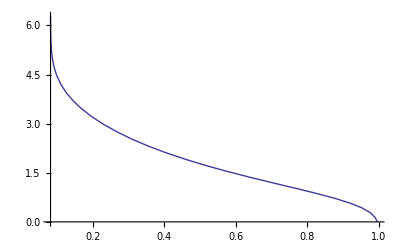

```mathematica
ListLinePlot[ans,PlotRange->All]
```

```mathematica
Export["doc/richards/tests/data/rsc01_analytic.csv",ans,"Table"]
```

doc/richards/tests/data/rsc01_analytic.csv